numerov with  linear potential

```mathematica
(*Potential, desired max energy*)
V[s_]:=Abs[s];Subscript[ϵ, m]=20.;
(*determine grid*)
rturn=FindRoot[V[s]==Subscript[ϵ, m],{s,Subscript[ϵ, m]}]⟦1,2⟧;d=1/(√(2 Subscript[ϵ, m]));
n=Round[2(rturn/d+4π )];s=Table[-(d (n+1))/2+d i,{i,n}];
(*calculate KE matrix*)
𝕀[n_,d_]:=DiagonalMatrix[1+0Range[n-Abs[d]],d];
B=1./12(𝕀[n,-1]+10 𝕀[n,0]+𝕀[n,1]);
A=1/d^2(𝕀[n,-1]-2 𝕀[n,0]+𝕀[n,1]);
KE=-1/2 Inverse[B].A;
(*Hamiltonian*)
H=KE+DiagonalMatrix[V[s]];
(*Energies, wavefunctions*)
{eval,evec}=Eigensystem[H];
```

Theoretical Eigenvalues

```mathematica
rootsa=Table[N[-2^(-1/3)*AiryAiZero[n]],{n,1,65}];
AiryAiPrimeZeros=DeleteDuplicates[Sort[Table[-2^(-1/3)*x/.FindRoot[AiryAiPrime[x],{x,-n+n/2}],{n,2,100}]],#1==#2 &];
zeros=Sort[Flatten[Append[rootsa,AiryAiPrimeZeros]]];
zeross=Delete[zeros,1];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Theoretical Eigenfunctions

```mathematica
(*Normalization Constants for first 65 eigenfunctions*)
```

```mathematica
AAA=Table[(2^(2/3)*Integrate[AiryAi[x]^2,{x,-2^(1/3)*zeross[[n]],∞}])^-0.5,{n,1,65}];
```

```mathematica
psiith[n_,s_]:=Piecewise[{{AAA[[n]]*AiryAi[2^(1/3)*(s-zeross[[n]])],s>0},{(-1)^(n+1)*AAA[[n]]*AiryAi[2^(1/3)*(-s-zeross[[n]])],s<0}}]
```

```mathematica
theory=Plot[psiith[50,s],{s,-22,22}];
f[i_]:=-(d (n+1))/2 +d i
scale=Map[f,Range[Length[evec[[-50]]]]];
result=Transpose[{scale,evec[[-50]]/√d}];
numerov=ListPlot[result,PlotRange->All];
```

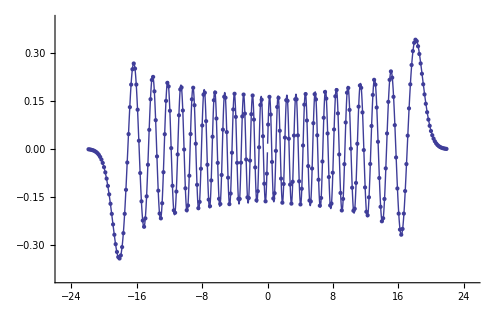

```mathematica
p1=Show[numerov,theory,ImageSize->500,LabelStyle->(FontSize->16),PlotRange->{{-25,25},{-0.4,0.4}}]
```

```mathematica
res=evec[[-50]]/√d-Table[psiith[50,scale⟦m⟧],{m,Length[scale]}];
```

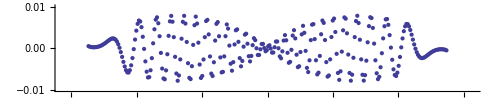

```mathematica
resplot=ListPlot[{scale,res}ᵀ,AspectRatio->0.2,ImageSize->500,LabelStyle->(FontSize->16),PlotRange->{{-25,25},{-0.01,0.01}}]
```